# Final Coding Project: Twitter Analysis

### By Joe Claire and Kate Gilman

Problem 1: Associations

```mathematica
twitter=ServiceConnect["Twitter"]
```

ServiceObject[…]

```mathematica
tweets=ServiceExecute[
twitter,
"TweetList",
{"Username"-> "benshapiro","MaxItems"->5000,"Elements"->"FullData"}];
```

Associations Problems

```mathematica
34.1
```

```mathematica
Values[Counts[Sort[IntegerDigits[3^100]]]];
```

```mathematica
34.2
```

```mathematica
BarChart[Values[Counts[Sort[IntegerDigits[2^1000]]]]];
```

```mathematica
34.3
```

```mathematica
BarChart[Counts[StringTake[ToLowerCase[WordList[]],1]]];
```

```mathematica
34.4
```

```mathematica
Reverse[Take[Sort[Counts[StringTake[ToLowerCase[WordList[]],1]]],-5]];
```

```mathematica
34.5
```

```mathematica
N[<|Counts[ToLowerCase[Characters[WikipediaData["computers"]]]]|>["q"]/<|Counts[ToLowerCase[Characters[WikipediaData["computers"]]]]|>["u"]];
```

```mathematica
34.6
```

```mathematica
Keys[Take[Sort[Counts[ToLowerCase[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]]],-10]];
```

Problem 2: Sentiment

```mathematica
tweets2=Normal@tweets;
```

```mathematica
tweetTexts=<|tweets2[[#]]|>["Text"]&/@Range[Length[tweets2]];
```

```mathematica
tweetSentiments=Classify["Sentiment",#]&/@tweetTexts;
```

```mathematica
tweetPieChart=PieChart[Counts[tweetSentiments], ChartLabels-> {"Positive","Neutral","Negative"
},PlotLabel->Style["Sentiments of 5000 Ben Shapiro Tweets",Bold,15]];
```

```mathematica
tweetTextsPos=Select[tweetTexts,Classify["Sentiment",#]=="Positive"&];
```

```mathematica
tweetTextsNeg=Select[tweetTexts,Classify["Sentiment",#]=="Negative"&];
```

```mathematica
wcp=WordCloud[TextWords[DeleteStopwords[tweetTextsPos]],ImageSize->Medium,PlotLabel-> Style["Positive Words",Bold,Red,15]];
```

```mathematica
wcn=WordCloud[TextWords[DeleteStopwords[tweetTextsNeg]],ImageSize->Medium,PlotLabel-> Style["Negative Words",Bold,Red,15]];
```

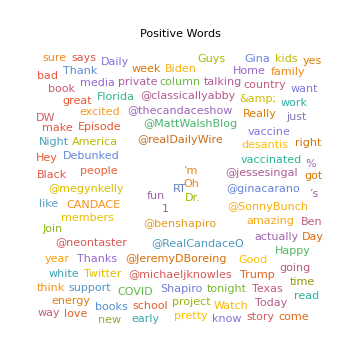
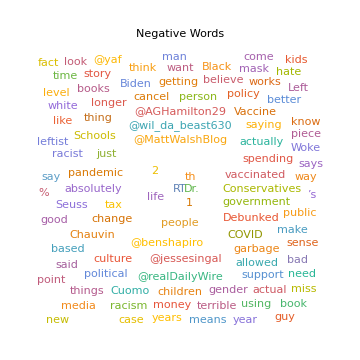

```mathematica
Framed[Row[{wcp,Spacer[50],wcn}]]
```

There seem to be more verbs on the positive side, whereas the negative side has more nouns and adjectives. When there are adjectives on the positive side, they are more positive words.

Problem 3: Comparing Corpora Through Log-odds Ratio

```mathematica
taylorswift13tweets=Normal@ServiceExecute[
twitter,
"TweetList",
{"Username"-> "taylorswift13","MaxItems"->1000,"Elements"->"FullData"}];
```

```mathematica
jpegmafiatweets=Normal@ServiceExecute[
twitter,
"TweetList",
{"Username"-> "darkskinmanson","MaxItems"->1000,"Elements"->"FullData"}];
```

```mathematica
N[Log2[((Values[Take[Reverse[Sort[wordfrequency1]],15]][[3]]+1)/(Length[wordfrequency1]+1))/((If[TrueQ[MemberQ[Keys[wordfrequency2],Keys[Take[Reverse[Sort[wordfrequency1]],15]][[3]]]],<|wordfrequency2|>[Keys[Take[Reverse[Sort[wordfrequency1]],15]][[3]]],0]+1)/(Length[wordfrequency2]+1))]]
```

0.35506

```mathematica
Reverse[Sort[wordfrequency1]];
```

```mathematica
Reverse[Sort[wordfrequency2]];
```

Numerator of Denominator:

```mathematica
If[TrueQ[MemberQ[Keys[wordfrequency2],Keys[Take[Reverse[Sort[wordfrequency1]],15]][[5]]]],<|wordfrequency2|>[Keys[Take[Reverse[Sort[wordfrequency1]],15]][[5]]],0]
```

58

```mathematica
N[((Values[Take[Reverse[Sort[wordfrequency1]],15]][[1]]+1)/(Length[wordfrequency1]+1))]
```

0.048211

```mathematica
(If[TrueQ[MemberQ[Keys[wordfrequency2],Keys[Take[Reverse[Sort[wordfrequency1]],15]][[1]]]],<|wordfrequency2|>[Keys[Take[Reverse[Sort[wordfrequency1]],15]][[1]]],0]+1)/(Length[wordfrequency2]+1)
```

1/2675

```mathematica
keyness[list1_,list2_,numberWord_]:= Module[{allwords1,allwords2,wordfrequency1,wordfrequency2,biglist},
allwords1=Flatten[ToLowerCase[TextWords[DeleteStopwords[<|list1[[#]]|>["Text"]&/@Range[Length[list1]]]]]];
allwords2=Flatten[ToLowerCase[TextWords[DeleteStopwords[<|list2[[#]]|>["Text"]&/@Range[Length[list2]]]]]];
wordfrequency1=Counts[allwords1];
wordfrequency2=Counts[allwords2];
biglist=Join[allwords1,allwords2];
BarChart[Flatten[{N[Log2[((Values[Take[Reverse[Sort[wordfrequency1]],numberWord]][[#]]+1)/(Length[wordfrequency1]+1))/((If[TrueQ[MemberQ[Keys[wordfrequency2],Keys[Take[Reverse[Sort[wordfrequency1]],numberWord]][[#]]]],<|wordfrequency2|>[Keys[Take[Reverse[Sort[wordfrequency1]],numberWord]][[#]]],0]+1)/(Length[wordfrequency2]+1))&/@Range[numberWord]]],N[-Log2[((Values[Take[Reverse[Sort[wordfrequency2]],numberWord]][[#]]+1)/(Length[wordfrequency2]+1))/((If[TrueQ[MemberQ[Keys[wordfrequency1],Keys[Take[Reverse[Sort[wordfrequency2]],numberWord]][[#]]]],<|wordfrequency1|>[Keys[Take[Reverse[Sort[wordfrequency2]],numberWord]][[#]]],0]+1)/(Length[wordfrequency1]+1))&/@Range[numberWord]]]}],
BarOrigin->Left,
ImageSize->Large,
ChartStyle->Flatten[{{Table[LightRed,numberWord]},{Table[LightBlue,numberWord]}}],ChartLabels->Placed[Join[Keys[Take[Reverse[Sort[wordfrequency1]],numberWord]],Keys[Take[Reverse[Sort[wordfrequency2]],numberWord]]],Before],
PlotLabel->Style[Row[{"Comparison of Top ",ToString[numberWord]," Tweet Words from ",Style[Row[{"@",ToString[<|list2|>["Username"]]}],FontColor->LightBlue]," and ",Style[Row[{"@",ToString[<|list1|>["Username"]]}],FontColor->LightRed]}],Bold,15]]]
```

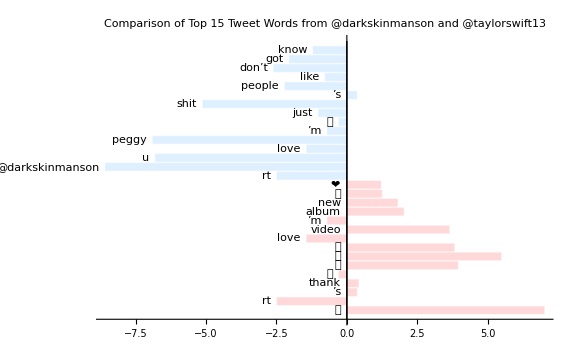

```mathematica
keyness[taylorswift13tweets,jpegmafiatweets,15]
```

Problem 4: Open-ended

1. How does the language used in tweets compare between Joe Biden’s personal Twitter account (@JoeBiden) vs his Presidential Twitter account (@POTUS)?

```mathematica
usernameInput[username1_,maxitemsnumber_]:=Normal@ServiceExecute[
twitter,
"TweetList",
{"Username"-> "@"<>ToString[username1],"MaxItems"->maxitemsnumber,"Elements"->"FullData"}]
```

```mathematica
potusTweets=usernameInput["POTUS",500];
```

```mathematica
joeBidenTweets=usernameInput["JoeBiden",500];
```

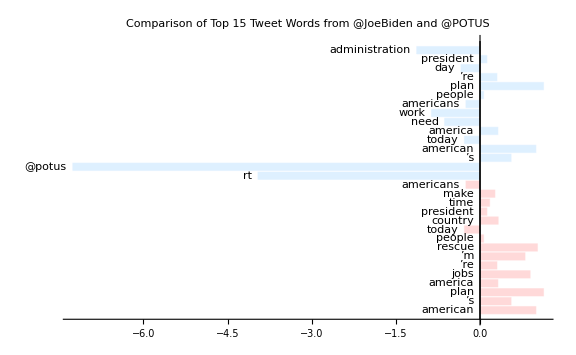

```mathematica
keyness[potusTweets,joeBidenTweets,15]
```

The language used by both accounts appears to be similar, though @JoeBiden is far more likely to retweet, and also often tags his other account @POTUS in his tweets. This may be because he is retweeting his @POTUS posts on @JoeBiden.

### 2. What are the similarities and differences between @SpaceX and @NASA’s Twitter language?

```mathematica
nasaTweets=usernameInput["NASA",3000];
```

```mathematica
spaceXTweets=usernameInput["SpaceX",3000];
```

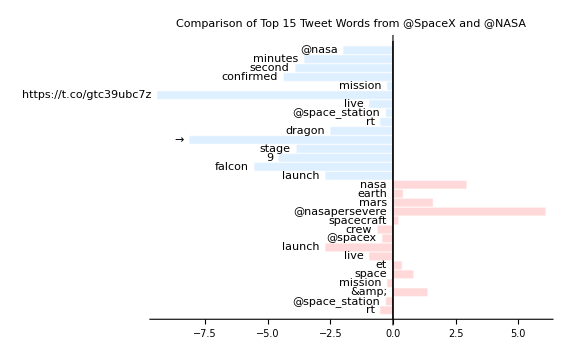

```mathematica
keyness[nasaTweets,spaceXTweets,15]
```

There is a good amount of overlap between these two Twitter accounts, but @SpaceX uses more consistent language. It is interesting to note that @SpaceX is more likely to tag @NASA than @NASA tagging @SpaceX.

### 3. How does comedic language compare between @rad_milk and @TheOnion?

```mathematica
onionTweets=usernameInput["TheOnion",3000];
```

```mathematica
radMilkTweets=usernameInput["rad_milk",3000];
```

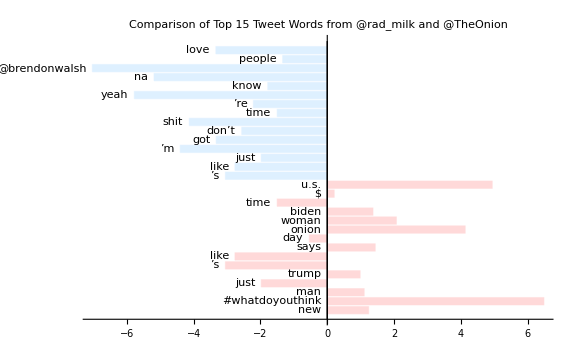

```mathematica
keyness[onionTweets,radMilkTweets,15]
```

The Onion discusses more political topics and uses language often seen in news headlines, whereas @rad_milk uses more informal language.